# Final Project : Summarization on Numerical Methods

By Breanna Dhautal | Due May 21

## Part I : Root Finding

## Bisection Method

### Let f(x) be a continuous function on [a,b] such that f(a)f(b). After N iterations of the bisection method, let x_n be the midpoint in the the N^th subinterval [a_n, b_n] |p_n - p| ≤ (b-a)/2^n , when n ≥ 1

#### We choose the function f(x) = x^3- x -1 on the interval [1,3]. The next two functions evaluate the bisection prediction, exact root, error, number of expected steps and the actual amount of steps it took, respectively.

```mathematica
a= 1;b=3;
tol = 0.01;
f[x_]:= x^3-x-1;
Bisection[f_, n_, ϵ_]:= Module[{ax =a, bx=b, cx,nx},
nx = 0;
Do[
cx= (ax+bx)/2;
If[f[ax]*f[cx]<0, bx=cx,ax=cx];
nx = nx+1;
If[ nx== n||  Abs[f[cx]]< ϵ, Break[]]
,n];
Return[{cx//N,nx}];
];
root[f_, ϵ_]:= Module[{broot, n0, exact, e, Nth},
Nth =2*Ceiling[Log[2, Abs[b-a]/ϵ]];
{broot, n0}= Bisection[f, Nth, ϵ];
exact = FindRoot[f[x], {x, a, b}, AccuracyGoal->5][[1,2]];
e = Abs[broot-exact];
Return[{ broot, exact, e, Nth, n0} //N]
];
root[f,tol]
```

{1.32422,1.32472,0.000499186,16.,9.}

The bisection root is  1.32422
The actual root is  1.32472 
The error is  0.000499186
The expected number of iterations is  16
The executed number of iterations is  9

#### Now we will create a graph comparing the actual root to the bisection generated root

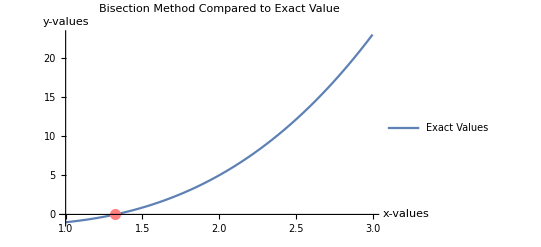

```mathematica
Plot[f[x], {x,1,3}, Epilog->{PointSize[0.02], Pink, Tooltip[#,#[[1]]] &@Point[{1.32422,f[1.32422]}]}, PlotLegends->{"Exact Values"}, AxesLabel->{"x-values","y-values"}, PlotLabel->"Bisection Method Compared to Exact Value"]
```

## Regula Falsi

### This method computes approximations in the same manner as the Secant method(seen later), but it includes a test to ensure that the root is always bracketed between successive iterations. It is generally a method that is used scarcely in comparison to the Secant Method |p_n - p| ≤ 1/2|a_n - b_n|

#### We choose the function f(x) = x^3- x -1 on the interval [1,3]. The next function evaluate the regula falsi prediction, exact root, error, number of expected steps and the actual amount of steps it took, respectively. Now we will create a function computing the predicted root:

```mathematica
a= 1;b=3;
tol = 0.01;
f[x_]:= x^3-x-1;
RegulaFalsi[f_,n_,ϵ_]:=Module[{nx, exact,rf,e, ax=a, bx=b},nx= 1;
Do[rf=NSolve[0== (f[ax]-f[bx])/(ax-bx)*(x-ax)+f[ax],x][[1,1,2]];
If[Abs[f[rf]]<ϵ, Break[];];If[f[rf]*f[bx]<0, ax=rf, bx=rf];nx= nx+1;,n];
exact = FindRoot[f[x], {x, ax, bx}, AccuracyGoal->5][[1,2]];
e = Abs[rf-exact];
Return[{rf, exact,e,nx}];];
RegulaFalsi[f,1000, tol]
```

{1.32239,1.32472,0.00232919,14}

The r- falsi root is  1.32239
The actual root is  1.32472 
The error is  0.00232919
The expected number of iterations is  16
The executed number of iterations is  14

#### Now we will create a graph comparing the actual root to the regula-falsi generated root

For the graph I altered the interval so the graph can be seen more clearly.

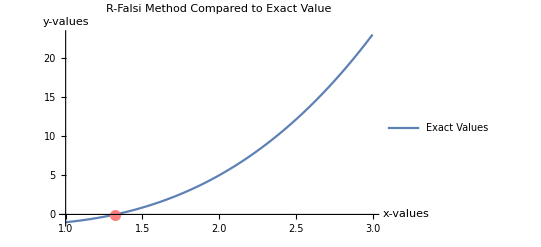

```mathematica
Plot[f[x], {x,1,3}, Epilog->{PointSize[0.02], Pink, Tooltip[#,#[[1]]] &@Point[{1.32239,f[1.32239]}]}, PlotLegends->{"Exact Values"}, AxesLabel->{"x-values","y-values"}, PlotLabel->"R-Falsi Method Compared to Exact Value"]
```

## Newtons Method

### This is one of the most powerful and well-known numerical methods for solving a root-finding problem. Newton’s method is derived by assuming that since | p − p_0| is small, the term involving ( p − p_0)^2 is much smaller, so p_n = p_(n-1) - (f(p_(n-1)))/(f '(p_(n-1))) , when n ≥ 1

#### Now we will create a function computing the predicted root:

```mathematica
a= 1;b=3;c=1;
tol = 0.01; n0=1;
f[x_]=Module[{}, x^3-x-1];
Newtons[x_]:= Module [{},N[x-(f[x]/f'[x]),3]];
nroot = Newtons[c];
Do[While[Abs[nroot-c] > tol,
n0++; 
c=nroot;
nroot = Newtons[c]
], 
{i,0, 20}];
nroot
n0
f[x_]:= x^3-x-1;
exact = FindRoot[f[x], {x, 1, 3}, AccuracyGoal->5];
e = Abs[nroot-1.32472];
e
```

1.

4

0.000480399

1.3252003989509068745`1.7448194874998537 is the value you obtain from the output, when you copy from the cell and past it to another it will reveal the other digits.

The Newton’s root is  1.32520
The actual root is  1.32472 
The error is  0.000480399
The expected number of iterations is  16
The executed number of iterations is  4

#### Now we will create a graph comparing the actual root to the Newton’s generated root

For the graph I altered the interval so the graph can be seen more clearly.

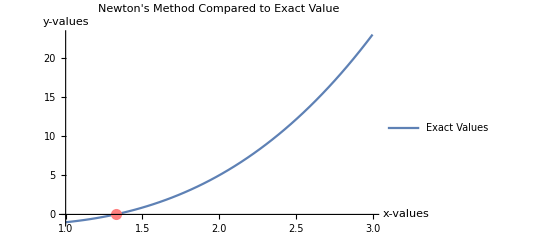

```mathematica
Plot[f[x], {x,1,3}, Epilog->{PointSize[0.02], Pink, Tooltip[#,#[[1]]] &@Point[{1.32520,f[1.32520]}]}, PlotLegends->{"Exact Values"}, AxesLabel->{"x-values","y-values"}, PlotLabel->"Newton's Method Compared to Exact Value"]
```

## Secants Method

### Newton’s method requires you to find the derivative after each step which is very complex to compute, therefore let’s give my kernel a break by using the Secant’s method! No more derivatives and here’s how: p_n = p_(n-1) - (f(p_(n-1))(p_(n-1)-p_(n-2)))/(f (p_(n-1))-f (p_(n-2))) , when n ≥ 1

#### We choose the function f(x) = x^3- x -1 with the initial guesses 1 and 3. Error tolerance = 0.01 Now we will create a function computing the predicted root:

```mathematica
f[x_]:= x^3-x-1;
exact = FindRoot[f[x], {x, 1, 3}, AccuracyGoal->5];
Secant[x1_,x2_] = N[x2-(f[x2]/((f[x2]-f[x1])/(x2-x1))),5];
n0 =1 ;
x1 = 1;
x2 =3;
x3 = Secant[x1,x2];
tol = 0.01;
Do[While[Abs[x3-x2] > tol,
n0++;
x1=x2;
x2 = x3;
x3 = Secant[x1,x2]],
{i,1,30}];
n0
N[x3]
err = Abs[N[x3]-1.32472];
err
```

2

1.33052

0.00579619

The Secant root is  1.33052
The actual root is  1.32472 
The error is  0.0057962
The expected number of iterations is  16
The executed number of iterations is  2

#### Now we will create a graph comparing the actual root to the Secant’s generated root

```mathematica
Plot[f[x], {x,1,3}, Epilog->{PointSize[0.02], Pink, Tooltip[#,#[[1]]] &@Point[{1.33052,f[1.33052]}]}, PlotLegends->{"Exact Values"}, AxesLabel->{"x-values","y-values"}, PlotLabel->"Newton's Method Compared to Exact Value"]
```

-Graphics-

## Fixed Point Iteration Method

### The number p is a fixed point for a given function g if g (p) = p. A fixed point for a function is a number at which the value of the function does not change when the function is applied. |p_n - p| ≤ k^n/(1-k)|p_1 - p_0|

#### We choose the function f[x_] = x^3-x-1 where we solve for f(p) = 0 p^3-p-1 = 0 p^3=p+1 p=(p+1)^(1/3)=g[p] with Error tolerance = 0.01

```mathematica
g[x_]:=N[(x+1)^(1/3)];
tol = 0.01;
p0 = 1;
n0=20;
i=1;
p = g[p0];
While[i ≤ n0,
p= g[p0];
If[Abs[p-p0] <tol,
Print["The approximation of the Fixed Point is: ",p ];
Print["The number of iterations required is: ", i];
Break[]];
i= i+1;
p0 = p
]
```

The approximation of the Fixed Point is: 1.32427

The number of iterations required is: 4

#### Now we compute the error followed by a graph to compare the results

```mathematica
f[x_]:= x^3-x-1;
exact = FindRoot[f[x], {x, 1, 3}, AccuracyGoal->5];
e = Abs[1.32427-1.32472];
e
```

0.00045

The Fixed Point root is  1.32427
The actual root is  1.32472 
The error is  0.00045
The expected number of iterations is  16
The executed number of iterations is  4

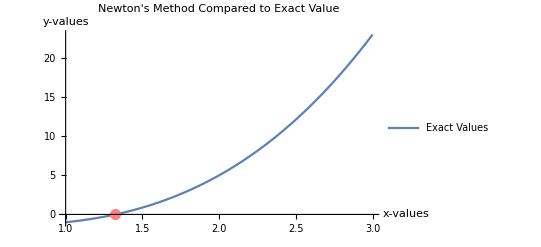

```mathematica
Plot[f[x], {x,1,3}, Epilog->{PointSize[0.02], Pink, Tooltip[#,#[[1]]] &@Point[{1.32427,f[1.32427]}]}, PlotLegends->{"Exact Values"}, AxesLabel->{"x-values","y-values"}, PlotLabel->"Newton's Method Compared to Exact Value"]
```

## Comparison of all the Methods

```mathematica
data = {{"Method","Predict Root","Exact Root","Error","Exp. Iterations","Act Iterations"},{"Bisection",1.32421875,1.324717935840947,0.0004991858409471028,16,9},{"Regula Falsi",1.322388752435362,1.3247179434399283,0.002329191004566411,16,14},{"Newton's",1.32520,1.3247179434399283,0.000480399,16,4},{"Secant",1.33052,1.3247179434399283,0.0057962,16,2},{"FPI",1.32427,1.3247179434399283,0.00045,16,4}};
Grid[data,ItemStyle->{Automatic,{1->{Bold,13}}},Frame->{All,1->True},Background->{None,{{LightCyan,LightYellow}}}]
```

### Here is a table for comparison

Method | Predict Root | Exact Root | Error | Exp. Iterations | Act Iterations
Bisection | 1.32422 | 1.32472 | 0.000499186 | 16 | 9
Regula Falsi | 1.32239 | 1.32472 | 0.00232919 | 16 | 14
Newton's | 1.3252 | 1.32472 | 0.000480399 | 16 | 4
Secant | 1.33052 | 1.32472 | 0.0057962 | 16 | 2
FPI | 1.32427 | 1.32472 | 0.00045 | 16 | 4

### Analysis

To compare which method is best we should uses the error considering we want the most accurate computation for the root done. The method’s were taught in a way that the last method was the best method to use, which is the fixed point iteration. The fixed point iteration has the lowest error value, followed by Newton’s, Bisection, Regula Falsi and lastly Secant Method. Regula Falsi took 14 iterations to compute the root, so that would automatically be ruled out to be used during a time dependent calculation. Secant was the quickest but had the highest error value. However it seems to be that the methods with 4 steps are the best because they have only 4 iterations, Fixed Point and Newton’s.

## Part II : Differential Equations

#### Evaluate y ’ = 3 + t − y, y(0) = 1 numerically on the interval [0,4]

## Euler’s Method

### Euler’s method is used to obtain approximations to the initial-value problem: (f(t,y))_ = dy/dt , when a ≤ t ≤ b Make the stipulation that the mesh points are equally distributed throughout the interval [a, b] choosing a positive integer N and selecting the mesh points: t_i = a +ih for every i= 0,1,2...N The common distance between the points, or the step size is: h = (b − a)/N = t_(i+1) - t_i Therefore the equation for Euler’s Method is : y_0 = α, y_(i+1) = y_i + h f( t_i, y_i)

### Here we will introduce the y[x], since we already are given y’[x]. Then we will compute Euler’s method on this at h=0.01 and at h=0.05 on the interval [0,4] Evaluate y ’ = 3 + t − y, y(0) = 1

```mathematica
EulerM[fun_,x0_,y0_,stepS_,xf_]:=(
t=x0; w=y0; totalS=(xf-x0)/stepS; For[i=0,i<totalS,i++,w=N[w+stepS*fun[t,w],32];t=t+stepS];Return[N[w,5]])
f[t_,y_]:=3+t−y;
fp[t_] := N[(2*ⅇ^t+t*ⅇ^t-1)/ⅇ^t,5];
Grid[
Join[{{"t","Euler h=0.05","Euler h=.01","Exact Value"}},
Table[{t,EulerM[f,0,1,0.05, t],EulerM[f,0,1,0.01, t],fp[t]},{t,{0,0.1,0.2,0.5,1,1.5,2}}]],Frame->All]
```

t | Euler h=0.05 | Euler h=.01 | Exact Value
0 | 1. | 1. | 1.
0.1 | 1.1975 | 1.19562 | 1.19516
0.2 | 1.38549 | 1.38209 | 1.38127
0.5 | 1.90126 | 1.89499 | 1.89347
1 | 2.64151 | 2.63397 | 2.63212
1.5 | 3.28536 | 3.27855 | 3.27687
2 | 3.87149 | 3.86602 | 3.86466

### Now we will graph the Euler’s method at h=0.01 and at h=0.05 on the interval [0,4], comparing it to the exact values.

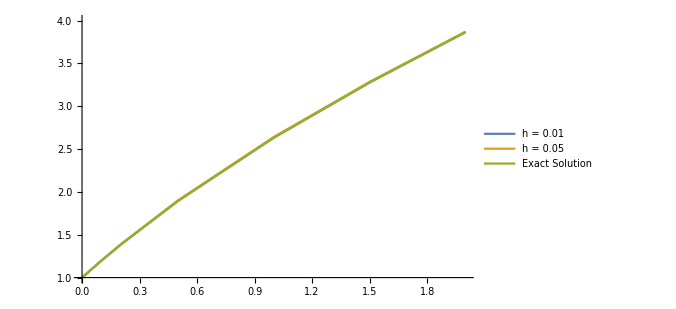

```mathematica
h01 = Table[{t,EulerM[f,0,1,0.01, t]},{t,{0,0.1,0.2,0.5,1,1.5,2}}];
h05 = Table[{t,EulerM[f,0,1,0.05, t]}, {t,{0,0.1,0.2,0.5,1,1.5,2}}];
exact1 = Table[{t,f[t]},{t,{0,0.1,0.2,0.5,1,1.5,2}}];
ListLinePlot[{h01,h05,exact1},PlotRange->{{0,2},{1,4}},PlotLegends->{"h = 0.01","h = 0.05", "Exact Solution" },ImageSize->500]
```

### Analysis

Graph comparing Euler’s at 0.01 and 0.05 both show very little difference to the exact solution which is why we can only see slight blue outlines on the graph, considering blue represents the exact solutions.  This ensures the calculation is being computed correctly.

## Backward Euler’s Method

### The Backward Euler one-step method is defined by: y_(i+1) = y_i + h f( t_(i+1), y_(i+1)) for i = 0,1,2,...,N

#### Evaluate y ’ = 3 + t − y, y(0) = 1 numerically on the interval [0,4]

```mathematica
BackwardEuler[fun_,x0_,y0_,stepS_,xf_]:=(
t=x0; w=y0; totalS=(xf-x0)/stepS; For[i=0,i<totalS,i++,w=N[w+stepS*fun[t+stepS,y[t+stepS]],32];t=t+stepS];Return[N[w,5]])
f[t_,y_]:=3+t−y;
fp[t_] := N[(2*ⅇ^t+t*ⅇ^t-1)/ⅇ^t,5];
Grid[
Join[{{"t","Backward Euler h=0.05","Backward Euler h=.01","Exact Value"}},
Table[{t,BackwardEuler[f,0,1,0.05, t],BackwardEuler[f,0,1,0.01, t],fp[t]},{t,{0,0.1,0.2,0.5,1,1.5,2}}]],Frame->All]
```

t | Backward Euler h=0.05 | Backward Euler h=.01 | Exact Value
0 | 1. | 1. | 1.
0.1 | 1.1928 | 1.19469 | 1.19516
0.2 | 1.37678 | 1.38036 | 1.38127
0.5 | 1.88371 | 1.89151 | 1.89347
1 | 2.61645 | 2.62897 | 2.63212
1.5 | 3.25761 | 3.27299 | 3.27687
2 | 3.84323 | 3.86035 | 3.86466

### Now we will graph the Backwards Euler’s method at h=0.01 and at h=0.05 on the interval [0,4], comparing it to the exact values.

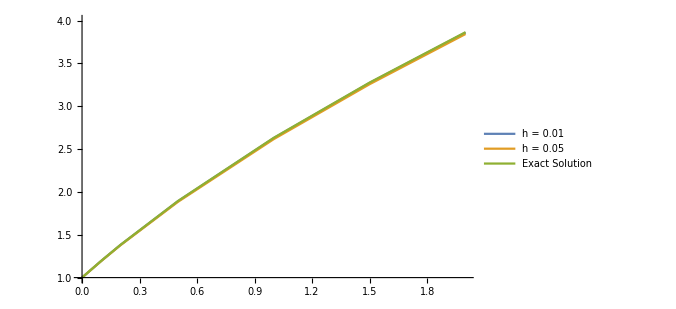

```mathematica
h01 = Table[{t,BackwardEuler[f,0,1,0.01, t]},{t,{0,0.1,0.2,0.5,1,1.5,2}}];
h05 = Table[{t,BackwardEuler[f,0,1,0.05, t]}, {t,{0,0.1,0.2,0.5,1,1.5,2}}];
exact1 = Table[{t,f[t]},{t,{0,0.1,0.2,0.5,1,1.5,2}}];
ListLinePlot[{h01,h05,exact1},PlotRange->{{0,2},{1,4}},PlotLegends->{"h = 0.01","h = 0.05", "Exact Solution" },ImageSize->500]
```

### Analysis

Graph comparing Backwards Euler’s at 0.01 and 0.05 both show very little difference to the exact solution which is why we mainly the blue line on the graph, considering blue represents the exact solutions. However as we increase the x value we see more orange which represents the 0.05 step.  This shows the 0.05 deviates away from the exact solution, making Euler’s more desirable to use than Backward Euler’s where we barely see the other two step sizes.

## Improved Euler’s Method

### The Backward Euler one-step method is defined by: y_(i+1) = y_i + h f( t_(i+1), y_(i+1)) for i = 0,1,2,...,N

#### Evaluate y ’ = 3 + t − y, y(0) = 1 numerically on the interval [0,4] at h=0.01 and h=0.05

```mathematica
ImprovedEuler[fun_,x0_,y0_,stepS_,xf_]:=(
t=x0 ; w=y0; totalS=(xf-x0)/stepS; For[i=0,i<totalS,i++,w=N[w+stepS*(1/2)*(fun[t,w]+fun[t+stepS, w+stepS*fun[t,w]]),32] ; t=t+stepS];Return[N[w,5]])
f[t_,y_]:=3+t−y;
fp[t_] := N[(2*ⅇ^t+t*ⅇ^t-1)/ⅇ^t,5];
Grid[
Join[{{"t","Improved Euler h=0.05","Improved Euler h=.01","Exact Value"}},
Table[{t,ImprovedEuler[f,0,1,0.05, t],ImprovedEuler[f,0,1,0.01, t],fp[t]},{t,{0,0.1,0.2,0.5,1,1.5,2}}]],Frame->All]
```

t | Improved Euler h=0.05 | Improved Euler h=.01 | Exact Value
0 | 1. | 1. | 1.
0.1 | 1.19512 | 1.19516 | 1.19516
0.2 | 1.3812 | 1.38127 | 1.38127
0.5 | 1.89334 | 1.89346 | 1.89347
1 | 2.63196 | 2.63211 | 2.63212
1.5 | 3.27673 | 3.27686 | 3.27687
2 | 3.86455 | 3.86466 | 3.86466

### Now we will graph the Improved Euler’s method at h=0.01 and at h=0.05 on the interval [0,4], comparing it to the exact values.

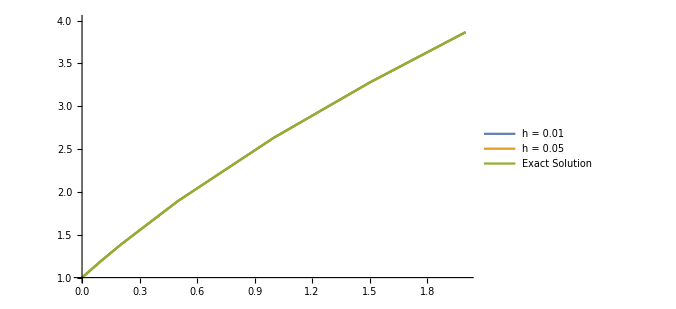

```mathematica
h01 = Table[{t,ImprovedEuler[f,0,1,0.01, t]},{t,{0,0.1,0.2,0.5,1,1.5,2}}];
h05 = Table[{t,ImprovedEuler[f,0,1,0.05, t]}, {t,{0,0.1,0.2,0.5,1,1.5,2}}];
exact1 = Table[{t,f[t]},{t,{0,0.1,0.2,0.5,1,1.5,2}}];
ListLinePlot[{h01,h05,exact1},PlotRange->{{0,2},{1,4}},PlotLegends->{"h = 0.01","h = 0.05", "Exact Solution" },ImageSize->500]
```

### Analysis

Graph comparing Improved Euler’s at 0.01 and 0.05 both show very little difference to the exact solution which is why we can only see slight blue outlines on the graph, considering blue represents the exact solutions.  This ensures the calculation is being computed correctly.

## Runge Kutta Method

### Runge-Kutta methods have the high-order local truncation error of the Taylor methods but eliminate the need to compute and evaluate the derivatives of f (t, y). y_0 = α , k_1 = hf (t_i, y_i) k_2 = hf (t_i + h/2, 1/2k_1+y_i) k_3 = hf (t_i + h/2, 1/2k_2+y_i) k_4 = hf (t_(i+1), k_3+y_i) y_(i+1) = +y_i + 1/6(k_1 +2 k_2 +2 k_3 +k_4 )

#### Evaluate y ’ = 3 + t − y, y(0) = 1 numerically on the interval [0,4] at h=0.01 and h=0.05

```mathematica
Kutta[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; totalS=(xf-x0)/h;  For[i=0,i<totalS,i++,w= N[w+(h/6)*(fun[t,w]+2*fun[t+h/2,w+h/2*fun[t,w]]+2*fun[t+h/2,w+h/2*fun[t+h/2,w+h/2*fun[t,w]]]+fun[t+h,w+h*fun[t+h/2,w+h/2*fun[t+h/2,w+h/2*fun[t,w]]]]),32];t=t+h];Return[N[w,9]])
f[t_,y_]:=3+t−y;
fp[t_] := N[(2*ⅇ^t+t*ⅇ^t-1)/ⅇ^t,9];
Kutta01 = Table[{t,Kutta[f,0,1,0.01,t]},{t,0,4,0.01}];
Kutta05 = Table[{t,Kutta[f,0,1,0.05,t]},{t,0,4,0.05}]; 
exact = Table[{t,fp[t]},{t,0,4,0.025}];
ListLinePlot[{Kutta01,Kutta05,exact},PlotRange->{{0,2},{1,4}},PlotLegends->{"h = 0.01","h = 0.05", "Exact Solution" },ImageSize->500]
```

### Now we will graph the Runge Kutta method at h=0.01 and at h=0.05 on the interval [0,4], comparing it to the exact values.

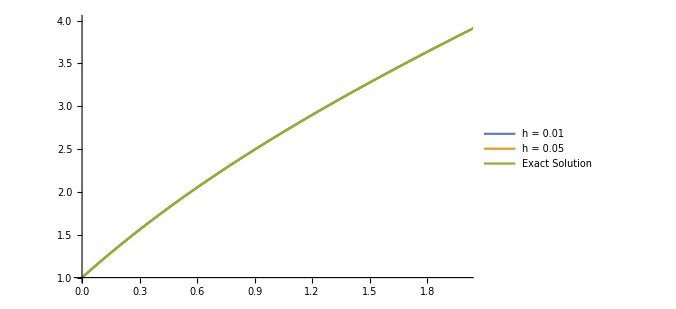

### Analysis

Graph comparing Runge Kutta at 0.01 and 0.05 both show very little difference to the exact solution which is why we can only see blue line on the graph, considering blue represents the exact solutions.  This ensures the calculation is being computed correctly.

## Adams Bashforth Implicit Method

### To derive an Adams-Bashforth explicit order technique, we form the backward difference polynomial. Some of the explicit multistep methods together with their required starting values and local truncation errors are as follows: Second Order Adams Bashforth

```mathematica
AB2[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; li = {w}; totalS=(xf-x0)/h; For[i=0,i<totalS,i++,If[i>0,w=N[w+(h/2)*(3*fun[t,w]-fun[t-h,li[[2]]]),32];li = Join[{w},li],w=N[w+h*fun[t,w],32];li = Join[{w},li]];t=t+h];Return[N[w,6]])
f[t_,y_]:=3+t−y;
fp[t_] := N[(2*ⅇ^t+t*ⅇ^t-1)/ⅇ^t,5];
AB201 = Table[{t,AB2[f,0,1,0.01,t]},{t,0,4,0.01}];
AB205 = Table[{t,AB2[f,0,1,0.05,t]},{t,0,4,0.05}]; 
exact = Table[{t,fp[t]},{t,0,4,0.001}];
ListLinePlot[{AB201,AB205 ,exact},PlotRange->{{0,2},{1,4}},PlotLegends->{"h = 0.01","h = 0.05", "Exact Solution" }]
```

### Now we will graph the Adams Bashforth of Second Order method at h=0.01 and at h=0.05 on the interval [0,4], comparing it to the exact values.

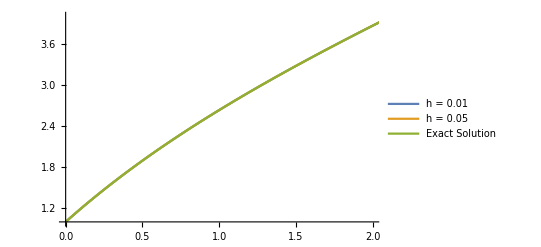

### To derive an Adams-Bashforth explicit order technique, we form the backward difference polynomial. Some of the explicit multistep methods together with their required starting values and local truncation errors are as follows: Fourth Order Adams Bashforth

```mathematica
AB4[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; li = {w}; totalS=(xf-x0)/h; For[i=0,i<totalS,i++,If[i>2,w=N[w+h/24*(55*fun[t,w]-59*fun[t-h,li[[2]]]+37*fun[t-2*h,li[[3]]]-9*fun[t-3*h,li[[4]]]),32];li = Join[{w},li],w=N[w+h*fun[t,w],32];li = Join[{w},li]];t=t+h];Return[N[w,6]])
f[t_,y_]:=3+t−y;
fp[t_] := N[(2*ⅇ^t+t*ⅇ^t-1)/ⅇ^t,5];
AB401 = Table[{t,AB4[f,0,1,0.01,t]},{t,0,4,0.01}];
AB405 = Table[{t,AB4[f,0,1,0.05,t]},{t,0,4,0.05}]; 
exact = Table[{t,fp[t]},{t,0,4,0.001}];
ListLinePlot[{AB401,AB405 ,exact},PlotRange->{{0,2},{1,4}},PlotLegends->{"h = 0.01","h = 0.05", "Exact Solution" }]
```

### Now we will graph the Adams Bashforth of Fourth Order method at h=0.01 and at h=0.05 on the interval [0,4], comparing it to the exact values.

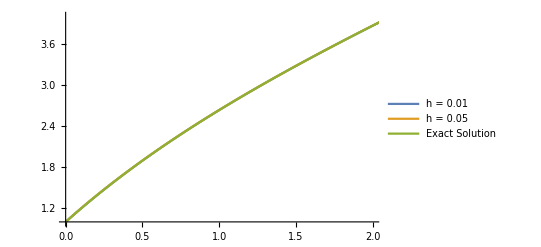

## Adams Moulton Explicit Method

### Implicit methods are derived by using (ti + 1, f (ti + 1, y (ti + 1))) as an additional interpolation node in the approximation of the integral ∫_t_i^(t_(i+1)) f(t, y(t))ⅆt Some of the more common implicit methods are as follows:

#### Second Order Adams Moulton

```mathematica
f[t_,y_]:=3+t−y;
fp[t_] := N[(2*ⅇ^t+t*ⅇ^t-1)/ⅇ^t,5];
AM2[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; totalS=(xf-x0)/h; For[i=0,i<totalS,i++,w=N[w+(h/2)*(fun[t+h,w+h*fun[t,w]]+fun[t,w]),32];t=t+h];Return[N[w,6]])
M201 = Table[{t,AM2[f,0,1,0.01,t]},{t,0,4,0.01}];
M205 = Table[{t,AM2[f,0,1,0.05,t]},{t,0,4,0.05}]; 
exact = Table[{t,fp[t]},{t,0,4,0.01}];
ListLinePlot[{M201,M205 ,exact},PlotRange->{{0,2},{1,4}},PlotLegends->{"h = 0.01","h = 0.05", "Exact Solution" }]
```

### Now we will graph the Adams Moulton of Second Order method at h=0.01 and at h=0.05 on the interval [0,4], comparing it to the exact values.

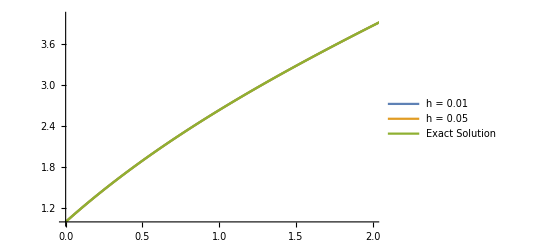

#### Fourth Order Adams Moulton

```mathematica
f[t_,y_]:=3+t−y;
fp[t_] := N[(2*ⅇ^t+t*ⅇ^t-1)/ⅇ^t,5];
AM4[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; li= {w}; totalS=(xf-x0)/h;  For[i=0,i<totalS,i++,If[i>1,w=N[w+h/24*(9*fun[t+h,w+h*fun[t,w]]+19*fun[t,w]-5*fun[t-h,li[[2]]]+fun[t-2*h,li[[3]]]),32];li = Join[{w},li],w=N[w+h*fun[t,w],32]; li = Join[{w},li]]; t=t+h];Return[N[w,6]])
M401 = Table[{t,AM4[f,0,1,0.01,t]},{t,0,4,0.01}];
M405 = Table[{t,AM4[f,0,1,0.05,t]},{t,0,4,0.05}]; 
exact = Table[{t,fp[t]},{t,0,4,0.01}];
ListLinePlot[{M401,M405 ,exact},PlotRange->{{0,2},{1,4}},PlotLegends->{"h = 0.01","h = 0.05", "Exact Solution" }]
```

### Now we will graph the Adams Moulton of Fourth Order method at h=0.01 and at h=0.05 on the interval [0,4], comparing it to the exact values.

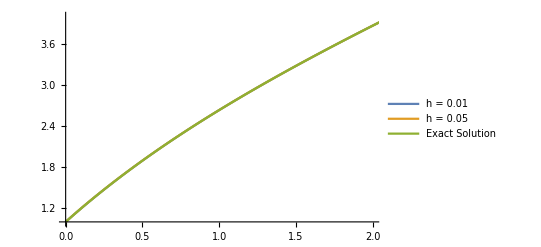

## Backward Differentiation Method

### Let it be noted that the first order Backward Differentiation method is essentially the backwards Euler formula. Below will be the second order and fourth order predictions

#### Second Order Backward Differentiation

```mathematica
BD2[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; li = {w}; totalS=(xf-x0)/h; For[i=0,i<totalS,i++,If[i>0,w=N[(1/3)*(4*w-li[[2]]+2*h*fun[t+h,w+h*fun[t,w]]),32];li = Join[{w},li],w=N[w+h*fun[t,w],32];li = Join[{w},li]];t=t+h];Return[N[w,6]])
f[t_,y_]:=3+t−y;
fp[t_] := N[(2*ⅇ^t+t*ⅇ^t-1)/ⅇ^t,5];
BD201 = Table[{t,BD2[f,0,1,0.01,t]},{t,0,4,0.01}];
BD205 = Table[{t,BD2[f,0,1,0.05,t]},{t,0,4,0.05}]; 
exact = Table[{t,fp[t]},{t,0,4,0.01}];
ListLinePlot[{M201,M205 ,exact},PlotRange->{{0,2},{1,4}},PlotLegends->{"h = 0.01","h = 0.05", "Exact Solution" }]
```

### Now we will graph the Second Order Backwards Differentiation method at h=0.01 and at h=0.05 on the interval [0,4], comparing it to the exact values.

-Graphics-

#### Fourth Order Backward Differentiation

```mathematica
BD4[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; li = {w}; totalS=(xf-x0)/h;   For[i=0,i<totalS,i++,If[i>2,w=N[(1/25)*(48*w-36*li[[2]]+16*li[[3]]-3*li[[4]]+12*h*fun[t+h,w+h*fun[t,w]]),32];li = Join[{w},li],w=N[w+h*fun[t,w],32];li = Join[{w},li]]; t=t+h];Return[N[w,6]])
f[t_,y_]:=3+t−y;
fp[t_] := N[(2*ⅇ^t+t*ⅇ^t-1)/ⅇ^t,5];
BD401 = Table[{t,BD4[f,0,1,0.01,t]},{t,0,4,0.01}];
BD405 = Table[{t,BD4[f,0,1,0.05,t]},{t,0,4,0.05}]; 
exact = Table[{t,fp[t]},{t,0,4,0.01}];
ListLinePlot[{BD401,BD405 ,exact},PlotRange->{{0,2},{1,4}},PlotLegends->{"h = 0.01","h = 0.05", "Exact Solution" }]
```

### Now we will graph the Fourth Order Backwards Differentiation method at h=0.01 and at h=0.05 on the interval [0,4], comparing it to the exact values.

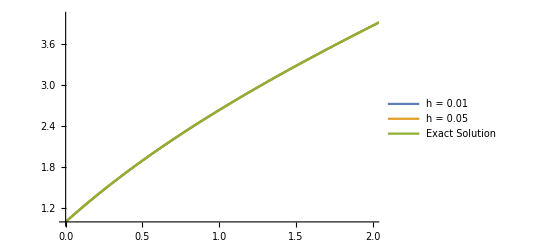

## Maximum Error!

### Now we will compute the maximum error at different h values to determine the best and worst method for our final part in our analysis.

```mathematica
EulerM[fun_,x0_,y0_,stepS_,xf_]:=(
t=x0; w=y0; totalS=(xf-x0)/stepS; For[i=0,i<totalS,i++,w=N[w+stepS*fun[t,w],32];t=t+stepS];Return[N[w,5]])
BackwardEuler[fun_,x0_,y0_,stepS_,xf_]:=(
t=x0; w=y0; totalS=(xf-x0)/stepS; For[i=0,i<totalS,i++,w=N[w+stepS*fun[t+stepS,y[t+stepS]],32];t=t+stepS];Return[N[w,5]])
ImprovedEuler[fun_,x0_,y0_,stepS_,xf_]:=(
t=x0 ; w=y0; totalS=(xf-x0)/stepS; For[i=0,i<totalS,i++,w=N[w+stepS*(1/2)*(fun[t,w]+fun[t+stepS, w+stepS*fun[t,w]]),32] ; t=t+stepS];Return[N[w,5]])
Kutta[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; totalS=(xf-x0)/h;  For[i=0,i<totalS,i++,w= N[w+(h/6)*(fun[t,w]+2*fun[t+h/2,w+h/2*fun[t,w]]+2*fun[t+h/2,w+h/2*fun[t+h/2,w+h/2*fun[t,w]]]+fun[t+h,w+h*fun[t+h/2,w+h/2*fun[t+h/2,w+h/2*fun[t,w]]]]),32];t=t+h];Return[N[w,9]])
AB2[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; li = {w}; totalS=(xf-x0)/h; For[i=0,i<totalS,i++,If[i>0,w=N[w+(h/2)*(3*fun[t,w]-fun[t-h,li[[2]]]),32];li = Join[{w},li],w=N[w+h*fun[t,w],32];li = Join[{w},li]];t=t+h];Return[N[w,6]])
AB4[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; li = {w}; totalS=(xf-x0)/h; For[i=0,i<totalS,i++,If[i>2,w=N[w+h/24*(55*fun[t,w]-59*fun[t-h,li[[2]]]+37*fun[t-2*h,li[[3]]]-9*fun[t-3*h,li[[4]]]),32];li = Join[{w},li],w=N[w+h*fun[t,w],32];li = Join[{w},li]];t=t+h];Return[N[w,6]])
AM2[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; totalS=(xf-x0)/h; For[i=0,i<totalS,i++,w=N[w+(h/2)*(fun[t+h,w+h*fun[t,w]]+fun[t,w]),32];t=t+h];Return[N[w,6]])
AM4[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; li= {w}; totalS=(xf-x0)/h;  For[i=0,i<totalS,i++,If[i>1,w=N[w+h/24*(9*fun[t+h,w+h*fun[t,w]]+19*fun[t,w]-5*fun[t-h,li[[2]]]+fun[t-2*h,li[[3]]]),32];li = Join[{w},li],w=N[w+h*fun[t,w],32]; li = Join[{w},li]]; t=t+h];Return[N[w,6]])
BD2[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; li = {w}; totalS=(xf-x0)/h; For[i=0,i<totalS,i++,If[i>0,w=N[(1/3)*(4*w-li[[2]]+2*h*fun[t+h,w+h*fun[t,w]]),32];li = Join[{w},li],w=N[w+h*fun[t,w],32];li = Join[{w},li]];t=t+h];Return[N[w,6]])
BD4[fun_,x0_,y0_,h_,xf_]:=(
t=x0; w=y0; li = {w}; totalS=(xf-x0)/h;   For[i=0,i<totalS,i++,If[i>2,w=N[(1/25)*(48*w-36*li[[2]]+16*li[[3]]-3*li[[4]]+12*h*fun[t+h,w+h*fun[t,w]]),32];li = Join[{w},li],w=N[w+h*fun[t,w],32];li = Join[{w},li]]; t=t+h];Return[N[w,6]])

f[t_,y_]:=3+t−y;
fp[t_] := N[(2*ⅇ^t+t*ⅇ^t-1)/ⅇ^t,5];Grid[Join[{{"h","Euler","Backwards Euler","Improved Euler","Runge Kutta", "Second A Moulton", "Fourth A Moulton","Second Backward","Fourth Backward"}},Table[{h,Max[Table[N[(Abs[fp[t]-EulerM[f,0,1,h,t]]),6],{t,0,4,h}]],Max[Table[N[(Abs[fp[t]-BackwardEuler[f,0,1,h,t]]),6],{t,0,4,h}]],Max[Table[N[(Abs[fp[t]-ImprovedEuler[f,0,1,h,t]]),6],{t,0,4,h}]],Max[Table[N[(Abs[fp[t]-Kutta[f,0,1,h,t]]),6],{t,0,4,h}]],Max[Table[N[(Abs[fp[t]-AM2[f,0,1,h,t]]),6],{t,0,4,h}]],Max[Table[N[(Abs[fp[t]-AM4[f,0,1,h,t]]),6],{t,0,4,h}]],Max[Table[N[(Abs[fp[t]-BD2[f,0,1,h,t]]),6],{t,0,4,h}]],Max[Table[N[(Abs[fp[t]-BD4[f,0,1,h,t]]),6],{t,0,4,h}]]},{h,{0.05, 0.01}}]],Frame->All]
```

### Analysis

The best method according to the large table output is Runge Kutta for both h= 0.05 and h=0.01. The maximum error was the lowest for the Runge Kutta Methods compared to the rest of methods. There fore Runge Kutta is the best, The Worst Method from the table is the method with the highest Maximum error which was Backwards Euler, which was seen earlier on in the table created.